Basic analysis of dumps captured from Android battery  ”uevent” interface

Phillip Stanley-Marbell
phillip.stanleymarbell@gmail.com / psm@mit.edu

February 2016

```mathematica
SetDirectory[NotebookDirectory[]];

analyze[deviceFamily_, fileName_] := Module[{grepBeforeCount, groupSize, currentIndex,
raw, rawGrouped,datesAndCurrentsMicroamps,datesAndDischargeCurrentsMicroamps,datesAndDischargeCurrentsAbsoluteMicroamps},

grepBeforeCount = If[deviceFamily == "nexus6p",
	15,
(* Else *)
	11];

groupSize = If[deviceFamily == "nexus6p",
	17,
(* Else *) 
	13];

currentIndex = If[deviceFamily == "nexus6p",
	16,
(* Else *)
	12];


raw =Import["!grep -B "<>ToString[grepBeforeCount]<>" 'POWER_SUPPLY_CURRENT_NOW' "<>fileName, "List"];
rawGrouped = Partition[raw, groupSize];(*Print[rawGrouped];*)
datesAndCurrentsMicroamps= {DateObject[#[[1]]], ToExpression[StringSplit[#[[currentIndex]], "="][[2]]]}&/@rawGrouped;
datesAndDischargeCurrentsMicroamps = Select[datesAndCurrentsMicroamps, #[[2]]≤ 0&];
datesAndDischargeCurrentsAbsoluteMicroamps = {#[[1]], Abs[#[[2]]]}&/@ datesAndDischargeCurrentsMicroamps;

DateListPlot[datesAndDischargeCurrentsAbsoluteMicroamps,
AspectRatio->1/3,
PlotTheme->"Detailed",
ImageSize->800,
Frame->True,
GridLines->{Automatic,None},
PlotStyle->{FontSize-> 18},
FrameLabel->{"Time", "Sampled Current (μA)"},
FrameStyle->{{Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Gray, Thickness[0.001]], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, LightGray]}, {Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, Black, Thick], Directive[FontFamily-> "Helvetica Neue",FontSize-> 16, GrayLevel[0.45], Thickness[0.0035]]}}]
];
```

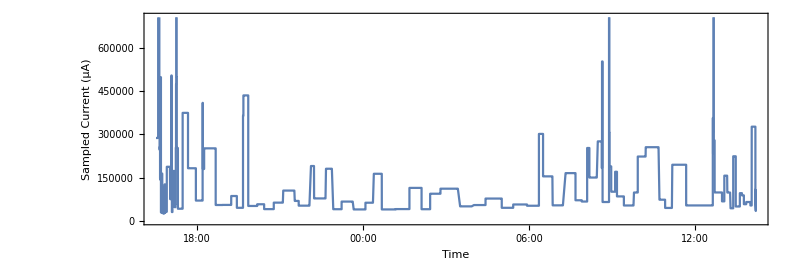

```mathematica
analyze["nexus6p", "../Logs/2016-02-03-14-15-47.txt"]
```